# Model 1: Plotting

This file contains the processing code for Model 1: Comparing Temporally Blind and Temporally Explicit Metrics. Before running this file, you must have extinction time and population size outputs from running Model 1 for both TPCs using Model1.nb; edit import and export locations (via ‘saveto’) for your own device.

## Load Data

Run import code before creating any figures. Edit import/export file names/locations for your local system and, if necessary, edit loaded parameter space to match your imported run. Default size is tmax2000_dims21,4,1,1000, corresponding with 1000 runs of 2000 time steps at each of 21 autocorrelation levels, 4 mean temperatures, and 1 standard deviation of temperature.

```mathematica
extTime=Import["/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/Model1/ExtMetrics8_Outputs/extMetrics8_extTime_tmax2000_dims21,4,1,1000.m","MX"];
p=Import["/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/Model1/ExtMetrics8_Outputs/extMetrics8_popsize_tmax2000_dims21,4,1,1000.m","MX"];

extTimeT=Import["/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/Model1/ExtMetrics8_Outputs/extMetrics8_trop_extTime_tmax2000_dims21,4,1,1000.m","MX"];
pT=Import["/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/Model1/ExtMetrics8_Outputs/extMetrics8_trop_popsize_tmax2000_dims21,4,1,1000.m","MX"];

tmax=2000; (*2000*)
maxsims=1000; (*1000*)
γvals=Range[0,2,.1];  (*21*)
μTvals=Range[23,26,1];  (*4*)
σTvals=Range[3,3,1]; (*1*)
```

## Calculate Temporally Blind Metrics

Calculate the expected population abundances given the means and standard deviation of temperature without any input from the simulations.

```mathematica
(*TEMPORATE - TPC1*)
gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=(gain[T]-loss[T])/.755; 

(* Parameters of the TPC model *)
TI=29;
β=180;
ma=0.000005;
mb=0.4;
mc=0.05;

α=.001;

(*array of temperatures for each parameter set*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

(*set initial pop size to mean pop size for each parameter set*)
ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]
N[ninit]

l23=ConstantArray[ninit[[1]],Length[γvals]];
l23t=Transpose[{γvals,Flatten[l23]}];
l24=ConstantArray[ninit[[2]],Length[γvals]];
l24t=Transpose[{γvals,Flatten[l24]}];
l25=ConstantArray[ninit[[3]],Length[γvals]];
l25t=Transpose[{γvals,Flatten[l25]}];
l26=ConstantArray[ninit[[4]],Length[γvals]];
l26t=Transpose[{γvals,Flatten[l26]}];

(*TROPICAL - TPC2*)
gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=(gain[T-2]-loss[T-2])/.4067; 

(* Parameters of the TPC model *)
TI=35;
β=130;
ma=0.000005;
mb=0.4;
mc=0.05;

α=.001;

(*array of temperatures for each parameter set*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

(*set initial pop size to mean pop size for each parameter set*)
ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

N[ninit]

lt23=ConstantArray[ninit[[1]],Length[γvals]];
lt23t=Transpose[{γvals,Flatten[lt23]}];
lt24=ConstantArray[ninit[[2]],Length[γvals]];
lt24t=Transpose[{γvals,Flatten[lt24]}];
lt25=ConstantArray[ninit[[3]],Length[γvals]];
lt25t=Transpose[{γvals,Flatten[lt25]}];
lt26=ConstantArray[ninit[[4]],Length[γvals]];
lt26t=Transpose[{γvals,Flatten[lt26]}];
```

{{851.715},{845.332},{797.846},{691.715}}

{{377.737},{444.963},{497.597},{520.587}}

## Process Simulation Data

Given the imported extinction times and population sizes, calculate the extinction metrics (abundance, stability, and probability of extinction) and create plotting arrays.

```mathematica
(*TEMPERATE*)
meansMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stdevsMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stabilityMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
extMatrix=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];

(*averaging over all timesteps before extinction within a simulation*)
Do[If[extTime[[i,j,1,l]]<tmax,extMatrix[[i,j,l]]=1,extMatrix[[i,j,l]]=0];
meansMatrix[[i,j,l]]=Mean[p[[i,j,1,l,2;;extTime[[i,j,1,l]]]]];
stdevsMatrix[[i,j,l]]=StandardDeviation[p[[i,j,1,l,2;;extTime[[i,j,1,l]]]]];
stabilityMatrix[[i,j,l]]=meansMatrix[[i,j,l]]/stdevsMatrix[[i,j,l]],
{l,1,maxsims},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*averaging across simulations with the same params*)
meansVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stdevsVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stabilityVals=ConstantArray[0,{Length[γvals],Length[μTvals]}];
propExt=ConstantArray[0,{Length[γvals],Length[μTvals]}];

Do[meansVals[[i,j]]=Mean[meansMatrix[[i,j]]];
stdevsVals[[i,j]]=Mean[stdevsMatrix[[i,j]]];
stabilityVals[[i,j]]=Mean[stabilityMatrix[[i,j]]];
propExt[[i,j]]=Total[extMatrix[[i,j]]/maxsims],
{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*create error data*)
meansError=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stdevsError=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stabilityError=ConstantArray[0,{Length[γvals],Length[μTvals]}];

Do[meansError[[i,j]]=StandardDeviation[meansMatrix[[i,j]]];
stdevsError[[i,j]]=StandardDeviation[stdevsMatrix[[i,j]]];
stabilityError[[i,j]]=StandardDeviation[stabilityMatrix[[i,j]]],
{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*TROPICAL*)
meansMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stdevsMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
stabilityMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];
extMatrixT=ConstantArray[0,{Length[γvals],Length[μTvals],maxsims}];

(*averaging over all timesteps before extinction within a simulation*)
Do[If[extTimeT[[i,j,1,l]]<tmax,extMatrixT[[i,j,l]]=1,extMatrixT[[i,j,l]]=0];
meansMatrixT[[i,j,l]]=Mean[pT[[i,j,1,l,2;;extTimeT[[i,j,1,l]]]]];
stdevsMatrixT[[i,j,l]]=StandardDeviation[pT[[i,j,1,l,2;;extTimeT[[i,j,1,l]]]]];
stabilityMatrixT[[i,j,l]]=meansMatrixT[[i,j,l]]/stdevsMatrixT[[i,j,l]],

{l,1,maxsims},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*averaging across simulations with the same params*)
meansValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stdevsValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stabilityValsT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
propExtT=ConstantArray[0,{Length[γvals],Length[μTvals]}];

Do[meansValsT[[i,j]]=Mean[meansMatrixT[[i,j]]];
stdevsValsT[[i,j]]=Mean[stdevsMatrixT[[i,j]]];
stabilityValsT[[i,j]]=Mean[stabilityMatrixT[[i,j]]];
propExtT[[i,j]]=Total[extMatrixT[[i,j]]/maxsims],
{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*create error data*)
meansErrorT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stdevsErrorT=ConstantArray[0,{Length[γvals],Length[μTvals]}];
stabilityErrorT=ConstantArray[0,{Length[γvals],Length[μTvals]}];

Do[meansErrorT[[i,j]]=StandardDeviation[meansMatrixT[[i,j]]];
stdevsErrorT[[i,j]]=StandardDeviation[stdevsMatrixT[[i,j]]];
stabilityErrorT[[i,j]]=StandardDeviation[stabilityMatrixT[[i,j]]],
{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*create plotting arrays*)
means23=Transpose[{γvals,Around@@@Transpose[{meansVals[[All,1]],meansError[[All,1]]}]}];
means24=Transpose[{γvals,Around@@@Transpose[{meansVals[[All,2]],meansError[[All,2]]}]}];
means25=Transpose[{γvals,Around@@@Transpose[{meansVals[[All,3]],meansError[[All,3]]}]}];
means26=Transpose[{γvals,Around@@@Transpose[{meansVals[[All,4]],meansError[[All,4]]}]}];

stability23=Transpose[{γvals,Around@@@Transpose[{stabilityVals[[All,1]],stabilityError[[All,1]]}]}];
stability24=Transpose[{γvals,Around@@@Transpose[{stabilityVals[[All,2]],stabilityError[[All,2]]}]}];
stability25=Transpose[{γvals,Around@@@Transpose[{stabilityVals[[All,3]],stabilityError[[All,3]]}]}];
stability26=Transpose[{γvals,Around@@@Transpose[{stabilityVals[[All,4]],stabilityError[[All,4]]}]}];

propExt23=Transpose[{γvals,propExt[[All,1]]}];
propExt24=Transpose[{γvals,propExt[[All,2]]}];
propExt25=Transpose[{γvals,propExt[[All,3]]}];
propExt26=Transpose[{γvals,propExt[[All,4]]}];

means23T=Transpose[{γvals,Around@@@Transpose[{meansValsT[[All,1]],meansErrorT[[All,1]]}]}];
means24T=Transpose[{γvals,Around@@@Transpose[{meansValsT[[All,2]],meansErrorT[[All,2]]}]}];
means25T=Transpose[{γvals,Around@@@Transpose[{meansValsT[[All,3]],meansErrorT[[All,3]]}]}];
means26T=Transpose[{γvals,Around@@@Transpose[{meansValsT[[All,4]],meansErrorT[[All,4]]}]}];

stabilityT23=Transpose[{γvals,Around@@@Transpose[{stabilityValsT[[All,1]],stabilityErrorT[[All,1]]}]}];
stabilityT24=Transpose[{γvals,Around@@@Transpose[{stabilityValsT[[All,2]],stabilityErrorT[[All,2]]}]}];
stabilityT25=Transpose[{γvals,Around@@@Transpose[{stabilityValsT[[All,3]],stabilityErrorT[[All,3]]}]}];
stabilityT26=Transpose[{γvals,Around@@@Transpose[{stabilityValsT[[All,4]],stabilityErrorT[[All,4]]}]}];

propExtT23=Transpose[{γvals,propExtT[[All,1]]}];
propExtT24=Transpose[{γvals,propExtT[[All,2]]}];
propExtT25=Transpose[{γvals,propExtT[[All,3]]}];
propExtT26=Transpose[{γvals,propExtT[[All,4]]}];
```

## Create Individual Plots

Code for each individual subplot. Outputs repressed for processing time.

```mathematica
meansPlot=ListLinePlot[{means23,means24,means25,means26,l23t,l24t,l25t,l26t},PlotStyle->{Lighter[Red],Red,Darker[Red],Black,{Dashed,Lighter[Red]},{Dashed,Red},{Dashed,Darker[Red]},{Dashed,Black}},PlotRange->{{-0.02,2.02},{450,1000}},  Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{None(*"Spectral Exponent γ"*),"Mean Population Abundance"},LabelStyle->Directive[Black],ImageSize->500] ;(*subplot a: temp means*)

meansPlotT=ListLinePlot[{means23T,means24T,means25T,means26T,lt23t,lt24t,lt25t,lt26t},PlotStyle->{Lighter[Red],Red,Darker[Red],Black,{Dashed,Lighter[Red]},{Dashed,Red},{Dashed,Darker[Red]},{Dashed,Black}},PlotRange->{{-0.02,2.02},{360,850}}, Frame->{True,True,False,False},FrameStyle->14,(*FrameLabel->{(*None,*)"Spectral Exponent γ","Mean Population Abundance"},*)LabelStyle->Directive[Black],ImageSize->500]; (*subplot d: trop means*)

stabilityPlot=ListLinePlot[{stability23,stability24,stability25,stability26},PlotStyle->{Lighter[Red],Red,Darker[Red],Black},PlotRange->{{-0.02,2.02},{1.5,7.5}}, Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{None(*"Spectral Exponent γ"*),"Population Stability"},LabelStyle->Directive[Black],ImageSize->500]; (*subplot b: temp stability*)

stabilityPlotT=ListLinePlot[{stabilityT23,stabilityT24,stabilityT25,stabilityT26},PlotStyle->{Lighter[Red],Red,Darker[Red],Black},PlotRange->{{-0.02,2.02},{1.5,4}}, Frame->{True,True,False,False},FrameStyle->14,(*FrameLabel->{None(*"Spectral Exponent γ"*),"Population Stability"},*)LabelStyle->Directive[Black],ImageSize->500]; (*subplot e: trop stability*)

extinctionPlot=ListLinePlot[{propExt23,propExt24,propExt25,propExt26},PlotStyle->{Lighter[Red],Red,Darker[Red],Black},PlotRange->{{-0.02,2.02},Automatic}, Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Spectral Exponent γ","Probability of Extinction"},LabelStyle->Directive[Black],ImageSize->500]; (*subplot c: temp extinction*)

extinctionPlotT=ListLinePlot[{propExtT23,propExtT24,propExtT25,propExtT26},PlotStyle->{Lighter[Red],Red,Darker[Red],Black},PlotRange->{{-0.02,2.02},Automatic}, Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Spectral Exponent γ",None(*"Probability of Extinction"*)},LabelStyle->Directive[Black],ImageSize->500]; (*subplot f: trop extinction*)
```

## Fig 2: Extinction Metrics

Create Fig 2. Labeling and error bar shading added in Adobe Illustrator 2024.

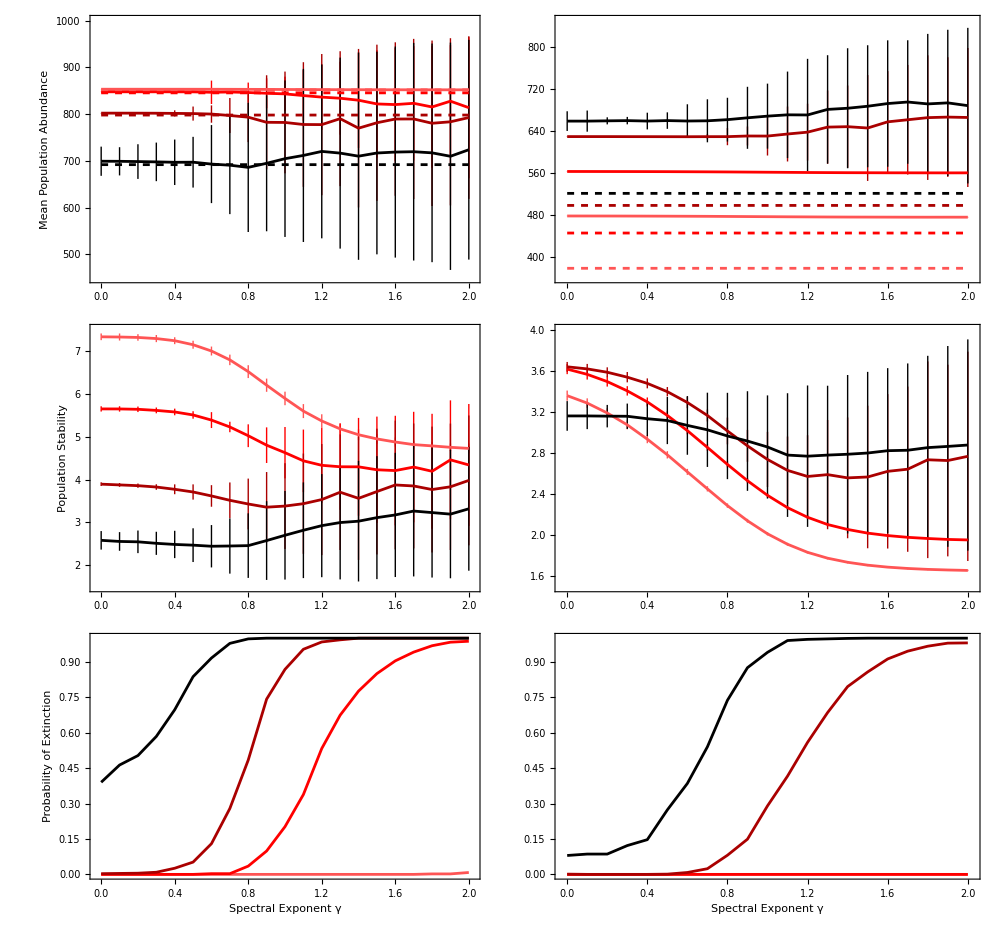

/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/ExtMetrics8_Outputs/fullStackedPlot.pdf

```mathematica
model1=GraphicsGrid[{{meansPlot,meansPlotT},{stabilityPlot,stabilityPlotT},{extinctionPlot,extinctionPlotT}},Spacings->{0,0},ImageSize->1000]

saveto="/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/Model1/ExtMetrics8_Outputs/"; (*edit export location here*)
Export[saveto<>"fullStackedPlot.pdf",model1,ImageResolution->1000]
```